## Brian — PS 9 — 2025-02-21 — Solution

## EIWL3 Sections 23, 24, and 25

## Exercises from EIWL3 Section 23

```mathematica
(* 23.1 *) N[Sqrt[2],500]
```

1.4142135623730950488016887242096980785696718753769480731766797379907324784621070388503875343276415727350138462309122970249248360558507372126441214970999358314132226659275055927557999505011527820605714701095599716059702745345968620147285174186408891986095523292304843087143214508397626036279952514079896872533965463318088296406206152583523950547457502877599617298355752203375318570113543746034084988471603868999706990048150305440277903164542478230684929369186215805784631115966687130130156185689872372

```mathematica
(* 23.2 *) RandomReal[1,10]
```

{0.961149,0.0834804,0.530357,0.515936,0.423071,0.00491769,0.0491434,0.133422,0.137943,0.381342}

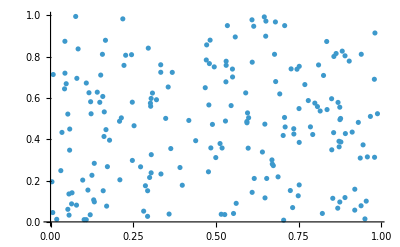

```mathematica
(* 23.3 *) ListPlot[RandomReal[1,{200,2}]]
```

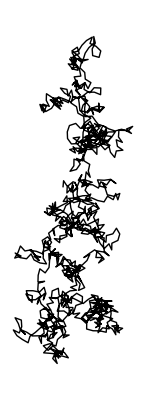

```mathematica
(* 23.4 *) Graphics[Line[AnglePath[RandomReal[2Pi,1000]]]]
```

```mathematica
(* 23.5 *) Table[Mod[n^2,10],{n,0,30}]
```

{0,1,4,9,6,5,6,9,4,1,0,1,4,9,6,5,6,9,4,1,0,1,4,9,6,5,6,9,4,1,0}

```mathematica
(* 23.6 *) Table[Mod[n^n,10],{n,100}]
```

{1,4,7,6,5,6,3,6,9,0,1,6,3,6,5,6,7,4,9,0,1,4,7,6,5,6,3,6,9,0,1,6,3,6,5,6,7,4,9,0,1,4,7,6,5,6,3,6,9,0,1,6,3,6,5,6,7,4,9,0,1,4,7,6,5,6,3,6,9,0,1,6,3,6,5,6,7,4,9,0,1,4,7,6,5,6,3,6,9,0,1,6,3,6,5,6,7,4,9,0}

```mathematica
(* 23.7 *) Round[Table[Pi^i,{i,10}]]
```

{3,10,31,97,306,961,3020,9489,29809,93648}

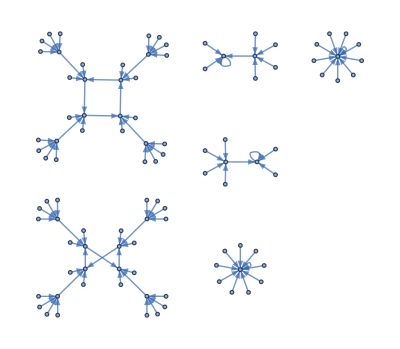

```mathematica
(* 23.8 *) Graph[Table[n->Mod[n^2,100],{n,0,99}]]
```

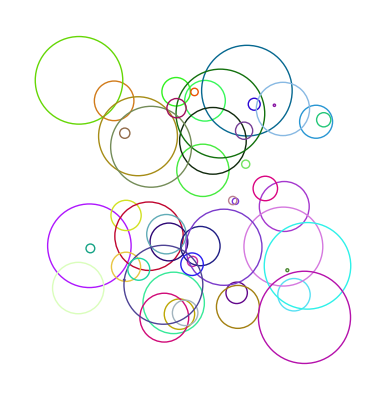

```mathematica
(* 23.9 *) Graphics[Table[
Style[Circle[{RandomReal[10],RandomReal[10]},RandomReal[2]],RandomColor[]],
50]]
(* This is an expression that is just complicated enough that I decided to use indenting to help me write it out correctly. *)
```

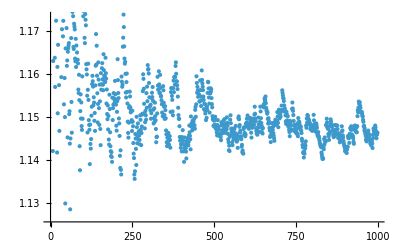

```mathematica
(* 23.10 *) ListPlot[Table[Prime[n]/(n Log[n]),{n,2,1000}]]
```

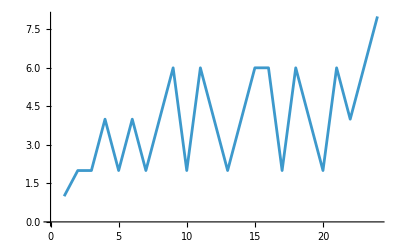

```mathematica
(* 23.11 *) ListLinePlot[Table[Prime[n]-Prime[n-1],{n,2,25}]]
(* I am not sure how we were supposed to know that the 25th prime was *)
(* the last one less than 100. I just did trial and error to figure that out. *)
```

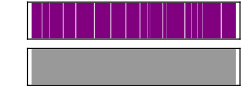

```mathematica
(* 23.12 *) Sound[Table[SoundNote[0, RandomReal[0.5]],20]]
```

## Exercises from EIWL3 Section 24

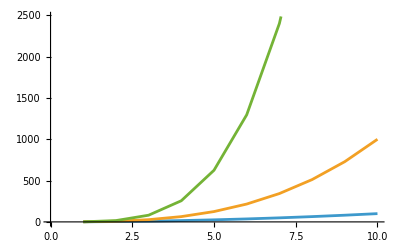

```mathematica
(* 24.1 *) ListLinePlot[{Range[10]^2,Range[10]^3,Range[10]^4}]
```

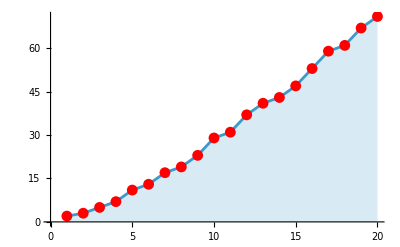

```mathematica
(* 24.2 *) ListLinePlot[Table[Prime[i],{i,20}],Filling->Axis,Mesh->All,MeshStyle->Red]
```

```mathematica
(* 24.3 *) ListPlot3D[GeoElevationData[GeoDisk[Entity["Mountain","FujiSan"],Quantity[20, "Miles"]]],PlotRange->All]
```

-Graphics3D-

```mathematica
(* 24.4 *) ReliefPlot[GeoElevationData[GeoDisk[Entity["Mountain","FujiSan"],Quantity[100, "Miles"]]]]
```

-Graphics-

```mathematica
(* 24.5 *) ListPlot3D[Table[Mod[i,j],{i,100},{j,100}]]
```

-Graphics3D-

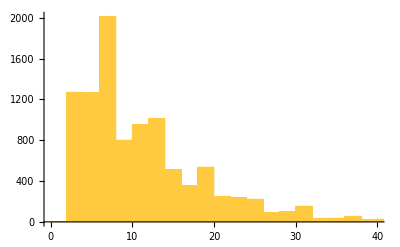

```mathematica
(* 24.6 *) Histogram[Table[Prime[j+1]-Prime[j],{j,9999}]]
```

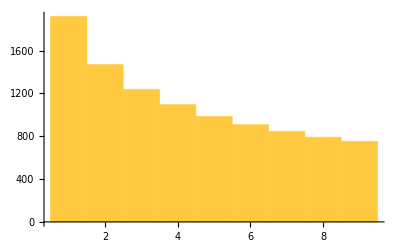

```mathematica
(* 24.7 *) Histogram[Table[First[IntegerDigits[j^2]],{j,10000}]]
```

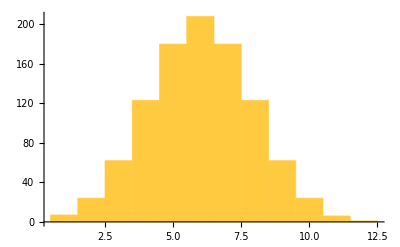

```mathematica
(* 24.8 *) Histogram[Table[StringLength[RomanNumeral[i]],{i,1000}]]
```

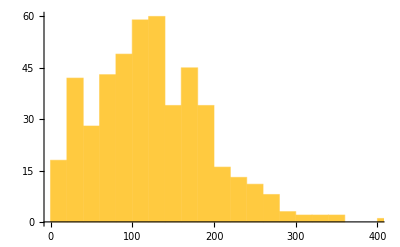

```mathematica
(* 24.9 *) Histogram[StringLength[TextSentences[WikipediaData["Computers"]]]]
```

```mathematica
(* 24.10 *) Table[Table[Total[RandomReal[100.0,n]],2],{n,1,5}]
```

{{40.8522,14.8525},{118.795,149.493},{90.923,160.367},{187.113,244.849},{202.133,157.38}}

```mathematica
(* 24.11 *) ListPlot3D[ImageData[Binarize[Graphics[Style[Text["W"],200]]]]]
```

-Graphics3D-

## Exercises from EIWL3 Section 25

```mathematica
(* 25.1 *) f/@Range[5]
```

{f[1],f[2],f[3],f[4],f[5]}

```mathematica
(* This is indeed the same result as *) Table[f[n],{n,5}]
(* We now eschew the bloated code we first learned. *)
(* This is going to eliminate a lot of our uses of Table[]. *)
```

{f[1],f[2],f[3],f[4],f[5]}

```mathematica
(* 25.2 *)f/@g/@Range[10]
```

{f[g[1]],f[g[2]],f[g[3]],f[g[4]],f[g[5]],f[g[6]],f[g[7]],f[g[8]],f[g[9]],f[g[10]]}

```mathematica
(* 25.3 *)x//d//c//b//a
```

a[b[c[d[x]]]]

```mathematica
(* This is indeed the same result as *) a[b[c[d[x]]]]
```

a[b[c[d[x]]]]

```mathematica
(* 25.4 *) Framed/@Alphabet[]
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

```mathematica
(* 25.5 *)ColorNegate/@ EntityClass["Planet",All][EntityProperty["Planet","Image"]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(* 25.6 *) GeoGraphics/@EntityList[EntityClass["Country","GroupOf5"]]
(* We learned about EntityList[] back in Section 16, *)
(* but I will be frank and admit that I could not *)
(* remember that I first needed to call EntityList[], *)
(* and even more frankly, I'll admit that I am still *)
(* unclear when EntityList[] and EntityValue are needed. *)
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(* 25.7 *) Binarize/@EntityClass["Country","Europe"][EntityProperty["Country","Flag"]]//ImageCollage
```

-Graphics-

```mathematica
(* 25.8 *) Column/@DominantColors/@ EntityClass["Planet",All][EntityProperty["Planet","Image"]]
```

{GrayLevel[0.0003583302785574673]
GrayLevel[0.37819453023602134]
GrayLevel[0.6046533866694355],RGBColor[0.8853258461241997, 0.6847278045450479, 0.4256700402289714]
RGBColor[0.000642062052308579, 0.001403728557887932, 0.0007410746962000475],RGBColor[0.0024606903915941458, 0.002409786977322984, 0.003967391669501376]
RGBColor[0.38137481479305974, 0.40751891927937794, 0.4878718697498957]
RGBColor[0.7093695751573504, 0.7271479152421573, 0.8068003834919311]
RGBColor[0.9792341072655132, 0.9822919456302736, 0.9938424502332899]
RGBColor[0.6354966433925654, 0.5479933929894801, 0.5436090390913342],RGBColor[0.0012177093066651906, 0.0015444381797393631, 0.002282631159508306]
RGBColor[0.5556976435501926, 0.4531266000126358, 0.33304542075624793]
RGBColor[0.97661432353462, 0.6748004218195973, 0.3694536477636728]
RGBColor[0.247985366921424, 0.2813954280094231, 0.26899240204489205]
RGBColor[0.4966218764141378, 0.5143298636117646, 0.5023898418540108]
RGBColor[0.6400489241717509, 0.7400325150547418, 0.8829327228050379],RGBColor[0.0007307420384636347, 0.0007454959245913933, 0.0016562167031508943]
RGBColor[0.678269963164705, 0.6320729858749744, 0.5998391342654895]
RGBColor[0.8542680892787012, 0.7080302078893711, 0.5495188294199109]
RGBColor[0.5603508711436291, 0.4463794016412469, 0.3598178300902997],RGBColor[0.0008759669414015513, 0.0006167590991106197, 0.001366050596437346]
RGBColor[0.3645501167535891, 0.34744090241667425, 0.30085819908851064]
RGBColor[0.6925169040198021, 0.6087670195382209, 0.4578034718491758]
RGBColor[0.9019996055101402, 0.7638467064934565, 0.49272539097128865],RGBColor[0.5487856307291583, 0.6154747806199766, 0.6457820783876971]
RGBColor[0.0026251717182227572, 0.0020772457357266776, 0.0024667841667845715]
RGBColor[0.22748358078321199, 0.24605669677627076, 0.25518636693604435],RGBColor[0.6462468675595785, 0.7691692304223126, 0.8252791002211531]
RGBColor[0.00014484531684443174, 0.00019326545709415257, 0.0002527639647539288]
RGBColor[0.42841487713890164, 0.5053577956882549, 0.5435623692316727]}

```mathematica
(* 25.9 *) Total[LetterNumber["Wolfram"]]
```

88